## Production via fragmentation

## Defining effective mixing angles

### Via mixing with π^0

```mathematica
Mel1=FeynmanRuleVertex[{"π^0","π^0","π^0","a"},{1,1,-1,-1},{"πm1","π0","πm2","a"}]/.{cvmd->0,pa->pπm1+pπ0-pπm2,coefPheavy->0}//Simplify//Contract;
Mel1=Mel1/.{ScalarProduct[pπ0,pπm1]->(s-2 mπ0^2)/2,ScalarProduct[pπ0,pπm2]->(2 mπ0^2-u)/2,ScalarProduct[pπm1,pπm2]->(2 mπ0^2-t)/2}/.{u->3 mπ0^2+ma^2-t-s}/.{ScalarProduct[pπ0,pπ0]->mπ0^2,ScalarProduct[pπm1,pπm1]->mπ0^2,ScalarProduct[pπm2,pπm2]->mπ0^2}//Simplify;
Mel1=D[Mel1,t]t+(Mel1/.{t->0})
Coefπ0=D[Mel1,π0ALP]/.{ηπ0->0,ηprπ0->0}//Simplify;
Θeff["π^0"]=1/Coefπ0 Mel1/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]//ruleLeadingOrderIsospin;
If[Simplify[D[Θeff["π^0"],κu]κu+D[Θeff["π^0"],κd]*κd]==0,Θeff["π^0"]=Θeff["π^0"]/.{κu->0,κd->0}]
exprnice=Simplify[D[Mel1/Coefπ0,π0ALP]π0ALP]+Simplify[D[Mel1/Coefπ0,cG]cG]+Simplify[D[Mel1/Coefπ0,ηprALP]ηprALP]+Simplify[D[Mel1/Coefπ0,ηALP]ηALP]/.{π0ALP->Subscript[θ, π a],cG->Subscript[c, G],κd->Subscript[κ, d],κu->Subscript[κ, u],ηALP->Subscript[θ, η a],ηπ0->Subscript[θ, η π],ηprπ0->Subscript[θ, η' π],ηprALP->Subscript[θ, η'a],ma->Subscript[m, a],mπ0->Subscript[m, π^0],cu->Subscript[c, u],cd->Subscript[c, d]}
exprnice//TeXForm;
```

-(mπ0^2 ϵ (δ (3 cG (√6 ηπ0+√3 ηprπ0+1) (κd+κu)+ηALP (6 ηπ0+3 √2 ηprπ0+√6)+ηprALP (3 √2 ηπ0+3 ηprπ0+√3))+3 cG (κd-κu)-3 π0ALP))/(3 fπ^2)

(δ (ma^2 mη^2 mηpr^2-2 ma^2 mη^2 mπ0^2-3 ma^2 mηpr^2 mπ0^2+4 ma^2 mπ0^4+mη^2 mπ0^4+2 mηpr^2 mπ0^4-3 mπ0^6) (3 cd ma^4-cd ma^2 mη^2-2 cd ma^2 mηpr^2+2 cG ma^2 mη^2+cG ma^2 mηpr^2-3 cG ma^2 mπ0^2-3 cG mη^2 mηpr^2+cG mη^2 mπ0^2+2 cG mηpr^2 mπ0^2-2 cs ma^2 mη^2+2 cs ma^2 mηpr^2+3 cu ma^4-cu ma^2 mη^2-2 cu ma^2 mηpr^2))/(3 (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ0^2) (mη^2-mπ0^2) (mηpr^2-mπ0^2))+(cd ma^2-cu ma^2)/(ma^2-mπ0^2)

-1/3 δ (3 θ_(π η')+3 √2 θ_(π η)+√3) θ_(a η')-1/3 δ θ_(a η) (3 √2 θ_(π η')+6 θ_(π η)+√6)+θ_(π a)+c_G (-κ_d-δ (κ_d+κ_u) (√3 θ_(π η')+√6 θ_(π η)+1)+κ_u)

-\frac{1}{3} \delta  \left(3 \theta _{\pi  \eta '}+3 \sqrt{2} \theta _{\pi  \eta }+\sqrt{3}\right) \theta _{a \eta '}-\frac{1}{3} \delta  \theta _{a \eta } \left(3 \sqrt{2} \theta _{\pi  \eta '}+6 \theta _{\pi  \eta }+\sqrt{6}\right)+\theta _{\pi 
   a}+c_G \left(-\kappa _d-\delta  \left(\kappa _d+\kappa _u\right) \left(\sqrt{3} \theta _{\pi  \eta '}+\sqrt{6} \theta _{\pi  \eta }+1\right)+\kappa _u\right)

### Via mixing with η

```mathematica
Mel2=FeynmanRuleVertex[{"π^0","π^0","η","a"},{1,1,-1,-1},{"π01","π02","η","a"}]/.{cvmd->0,pa->pπ01+pπ02-pη,coefPheavy->0}//Simplify//Contract;
Mel2=Mel2/.{ScalarProduct[pπ01,pπ02]->(s-2 mπ0^2)/2,ScalarProduct[pπ01,pπη]->(mπ0^2+mη^2-t)/2}/.{u->2 mπ0^2+mη^2+ma^2-t-s}//Simplify;
Mel2=D[Mel2,t]t+(Mel2/.{t->0})
Coefη=D[Mel2,ηALP];
Θeff["η"]=1/Coefη Mel2/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{ϵ->1}//ruleLeadingOrderIsospin;
If[Simplify[D[Θeff["η"],κu]κu+D[Θeff["η"],κd]*κd]==0,Θeff["η"]=Θeff["η"]/.{κu->0,κd->0}]
Simplify[D[Mel2/Coefη,ηALP]ηALP]+Simplify[D[Mel2/Coefη,cG]cG]+Simplify[D[Mel2/Coefη,ηprALP]ηprALP]+Simplify[D[Mel2/Coefη,π0ALP]π0ALP]/.{π0ALP->Subscript[θ, π a],cG->Subscript[c, G],κd->Subscript[κ, d],κu->Subscript[κ, u],ηALP->Subscript[θ, η a],ηπ0->Subscript[θ, η π],ηprπ0->Subscript[θ, η' π],ηprALP->Subscript[θ, η'a],ma->Subscript[m, a],mπ0->Subscript[m, π^0],cu->Subscript[c, u],cd->Subscript[c, d]}//TeXForm;
```

(mπ0^2 ϵ (cG δ ηπ0 κd-cG δ ηπ0 κu+2 √2 cG δ ηprπ0 κd-2 √2 cG δ ηprπ0 κu+√6 cG δ κd-√6 cG δ κu+√6 cG κd+√6 cG κu-δ ηπ0 π0ALP-2 √2 δ ηprπ0 π0ALP-√6 δ π0ALP+2 ηALP+√2 ηprALP))/(3 fπ^2)

1/2 (2 ((cG (√(2/3) ma^2+√(2/3) (mπ0^2-2 mη^2)))/(ma^2-mη^2)-(√(2/3) ma^2 (cd-cs+cu))/(ma^2-mη^2))-(√(2/3) (cd ma^2+2 cG ma^2-cG mηpr^2-cG mπ0^2+2 cs ma^2+cu ma^2))/(ma^2-mηpr^2))+1/2 (-(2 √(2/3) δ ma^2 mπ0^2 (cd-cu))/((ma^2-mη^2) (ma^2-mπ0^2))+(√(2/3) δ ma^2 mπ0^2 (cd-cu))/((ma^2-mπ0^2) (mη^2-mπ0^2))-(√(2/3) δ ma^2 mπ0^2 (cd-cu))/((ma^2-mηpr^2) (ma^2-mπ0^2))+(2 √(2/3) δ ma^2 mπ0^2 (cd-cu))/((ma^2-mπ0^2) (mηpr^2-mπ0^2))-(√6 δ ma^2 (cd-cu))/(ma^2-mπ0^2))

-\frac{1}{2} \delta  \theta _{\pi  a} \left(2 \sqrt{2} \theta _{\pi  \eta '}+\theta _{\pi  \eta }+\sqrt{6}\right)+\frac{\theta _{a \eta '}}{\sqrt{2}}+\theta _{a \eta }+\frac{1}{2} c_G \left(\kappa _d \left(\delta  \left(2 \sqrt{2} \theta _{\pi 
   \eta '}+\theta _{\pi  \eta }+\sqrt{6}\right)+\sqrt{6}\right)+\kappa _u \left(\sqrt{6}-\delta  \left(2 \sqrt{2} \theta _{\pi  \eta '}+\theta _{\pi  \eta }+\sqrt{6}\right)\right)\right)

### Via mixing with η’

```mathematica
Mel3=FeynmanRuleVertex[{"π^0","π^0","η'","a"},{1,1,-1,-1},{"π01","π02","ηpr","a"}]/.{cvmd->0,pa->pπ01+pπ02-pηpr,coefPheavy->0}//Simplify//Contract;
Mel3=Mel3/.{ScalarProduct[pπ01,pπ02]->(s-2 mπ0^2)/2,ScalarProduct[pπ01,pπη]->(mπ0^2+mηpr^2-t)/2}/.{u->2 mπ0^2+mηpr^2+ma^2-t-s}//Simplify;
Mel3=D[Mel3,t]t+(Mel3/.{t->0})
Coefηpr=D[Mel3,ηprALP];
Θeff["η'"]=1/Coefηpr Mel3/.rulem0aTransformationSymbolicToExplicit[choiceMixingDescription]/.{ϵ->1}//ruleLeadingOrderIsospin;
If[Simplify[D[Θeff["η'"],κu]κu+D[Θeff["η'"],κd]*κd]==0,Θeff["η'"]=Θeff["η'"]/.{κu->0,κd->0}]
Simplify[D[Mel3/Coefηpr,ηprALP]ηprALP]+Simplify[D[Mel3/Coefηpr,cG]cG]+Simplify[D[Mel3/Coefηpr,ηALP]ηALP]+Simplify[D[Mel3/Coefηpr,π0ALP]π0ALP]/.{π0ALP->Subscript[θ, π a],cG->Subscript[c, G],κd->Subscript[κ, d],κu->Subscript[κ, u],ηALP->Subscript[θ, η a],ηπ0->Subscript[θ, η π],ηprπ0->Subscript[θ, η' π],ηprALP->Subscript[θ, η'a],ma->Subscript[m, a],mπ0->Subscript[m, π^0],cu->Subscript[c, u],cd->Subscript[c, d]}//TeXForm;
```

(mπ0^2 ϵ (2 √2 cG δ ηπ0 κd-2 √2 cG δ ηπ0 κu-cG δ ηprπ0 κd+cG δ ηprπ0 κu+√3 cG δ κd-√3 cG δ κu+√3 cG κd+√3 cG κu-2 √2 δ ηπ0 π0ALP+δ ηprπ0 π0ALP-√3 δ π0ALP+√2 ηALP+ηprALP))/(3 fπ^2)

√2 ((cG (√(2/3) ma^2+√(2/3) (mπ0^2-2 mη^2)))/(ma^2-mη^2)-(√(2/3) ma^2 (cd-cs+cu))/(ma^2-mη^2))-(cd ma^2+ma^2 (2 cs+cu))/(√3 (ma^2-mηpr^2))-(2 δ ma^2 mπ0^2 (cd-cu))/(√3 (ma^2-mη^2) (ma^2-mπ0^2))+(4 δ ma^2 mπ0^2 (cd-cu))/(√3 (ma^2-mπ0^2) (mη^2-mπ0^2))-(δ ma^2 mπ0^2 (cd-cu))/(√3 (ma^2-mηpr^2) (ma^2-mπ0^2))-(δ ma^2 mπ0^2 (cd-cu))/(√3 (ma^2-mπ0^2) (mηpr^2-mπ0^2))-(√3 δ ma^2 (cd-cu))/(ma^2-mπ0^2)-(cG (2 ma^2-mηpr^2-mπ0^2))/(√3 (ma^2-mηpr^2))

\delta  \theta _{\pi  a} \left(\theta _{\pi  \eta '}-2 \sqrt{2} \theta _{\pi  \eta }-\sqrt{3}\right)+\theta _{a \eta '}+\sqrt{2} \theta _{a \eta }+c_G \left(\kappa _d \left(\delta  \left(-\theta _{\pi  \eta '}+2 \sqrt{2} \theta _{\pi  \eta
   }+\sqrt{3}\right)+\sqrt{3}\right)+\kappa _u \left(\delta  \left(\theta _{\pi  \eta '}-2 \sqrt{2} \theta _{\pi  \eta }-\sqrt{3}\right)+\sqrt{3}\right)\right)

## Definition for an arbitrary model

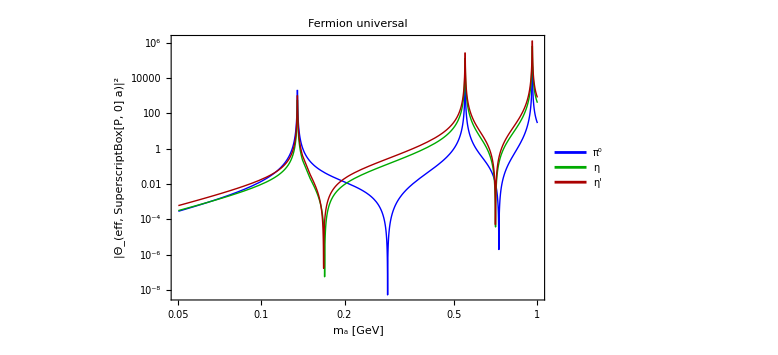
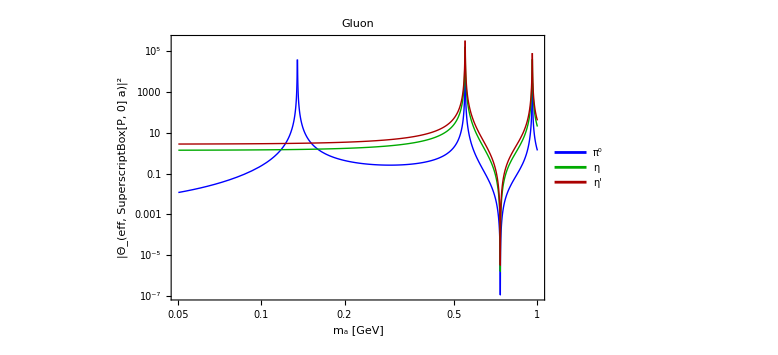
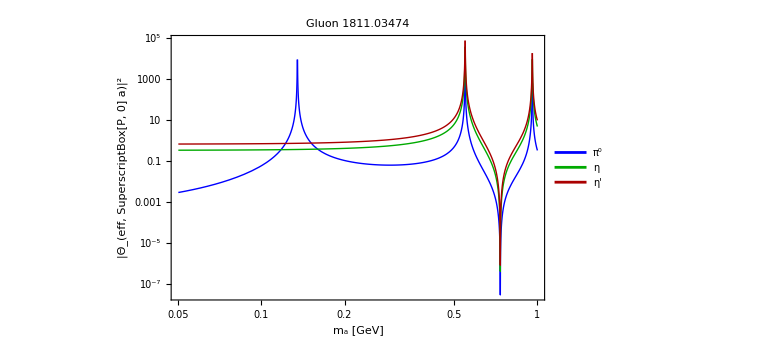
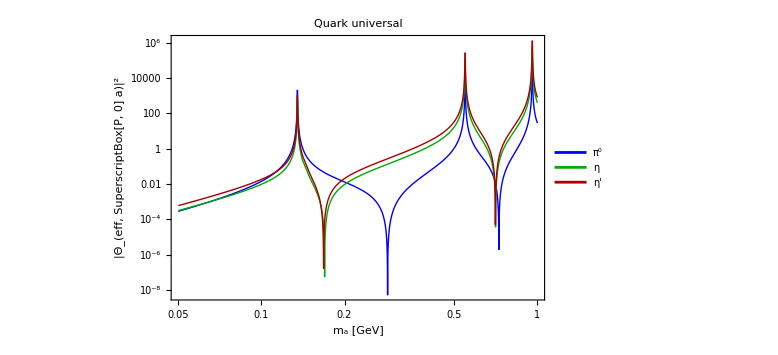
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Do[
{Θ2effModelΛ[ma_,model,Λ_,"π^0"],Θ2effModelΛ[ma_,model,Λ_,"η"],Θ2effModelΛ[ma_,model,Λ_,"η'"]}=ruleSymbolsToNumbersFinal[{Θeff["π^0"]^2,Θeff["η"]^2,Θeff["η'"]^2}/.tableValuesReplacement[model,Λ],2]//Simplify;
,{model,ModelListAll}]
rowExpl={{"ma [GeV]","theta2_eff,Pi0","theta2_eff,Eta","theta2_eff,EtaPr"}};
malist=Select[Table[ma,{ma,0.02,10.,0.0025}],!MemberQ[MASS[#]&/@{"π^0","η","η'"},#]&];
ΛChoice=10^3.;
Do[
func[ma_,model]=Join[{ma,Θ2effModelΛ[ma,model,ΛChoice,"π^0"],Θ2effModelΛ[ma,model,ΛChoice,"η"],Θ2effModelΛ[ma,model,ΛChoice,"η'"]}];
Tables=Join[rowExpl,Table[Re[func[ma,model]],{ma,malist}]];
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",model,"production","theta2_eff-"<>model<>"-Lambda="<>ToString[10^-3 ΛChoice]<>"-TeV.csv"}],Tables,"CSV"];
,{model,ModelListAll}]
plotslist=LogLogPlot[Evaluate[Drop[func[ma,#],1]],{ma,0.05,1},PlotRange->{{0.05,1},All},Frame->True,FrameLabel->{"m_a [GeV]","|Θ_(eff, SuperscriptBox[P, 0] a)|^2"},FrameStyle->Directive[Thick,Black,18],ImageSize->Large,PlotLabel->Style[Row[{#}],18,Black],PlotLegends->Placed[Style[#,20,Black]&/@listMesonP0,{0.07,0.2}],PlotStyle->({#,Thick}&/@{Blue,Darker@Green,Darker@Red})]&/@ModelListAll
θEffplot//Clear;
MapThread[(#1=#2)&,{θEffplot[#]&/@ModelListAll,plotslist}];
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"plots",#,"production","Theta2eff-fragmentation-"<>#<>".pdf"}],θEffplot[#]]&/@ModelListAll;
```

## Calculating the fluxes

### Integrated fluxes

{FermilabBD,LHC,SerpukhovBD,SPS}

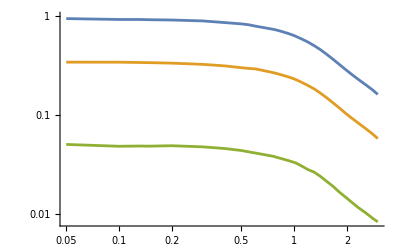

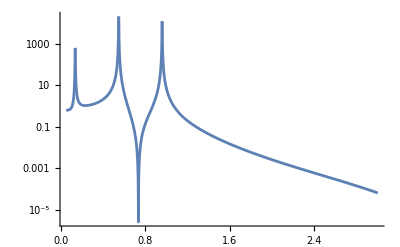

```mathematica
FluxFragmentationData=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","FluxFragmentation.mx"}],"MX"];
Do[
Module[{fac=FluxFragmentationData[[i]][[1]],mmin,mmax},
{mmin,mmax}=MinMax[FluxFragmentationData[[i]][[2]][[All,1]]];
{FluxFragmentation[ma_,"π^0",fac],FluxFragmentation[ma_,"η",fac],FluxFragmentation[ma_,"η'",fac]}=If[mmin<=ma<=mmax,Evaluate[(Interpolation[Log[Abs[FluxFragmentationData[[i]][[2]][[All,{1,#}]]]],InterpolationOrder->1][Log[ma]]//Exp)],0.]&/@{2,3,4};
Do[
PALPprod["Fragmentation",model,fac,ma_,f_,Λ_]=If[(FluxFragmentationData[[i]][[2]]//Min)<=ma<=(FluxFragmentationData[[i]][[2]]//Max),Evaluate[(Fπ/f)^2*Total[(Θ2effModelΛ[ma,model,Λ,#]*FluxFragmentation[ma,#,fac]&/@listMesonP0)]],0.];
,{model,ModelListAll}]
]
,{i,1,Length[FluxFragmentationData],1}];
FacilityListFragmentation=Keys[DownValues@FluxFragmentation][[All,1,-1]]//DeleteDuplicates
factest="FermilabBD";
LogLogPlot[Evaluate[FluxFragmentation[ma,#,factest]&/@listMesonP0],{ma,0.05,3}]
LogPlot[PALPprod["Fragmentation","Gluon",factest,ma,Fπ,10^3.],{ma,0.05,3}]
```

#### Exporting for SensCalc

```mathematica
(*Do[
Module[{Λchoice=10^3.},
modname=If[modelChoice=="Gluon","ALP-gluon",If[modelChoice=="Fermion universal","ALP-fermion",modelChoice]];
Export[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology",modelChoice,"For SensCalc","ProductionProbability-Fragmentation-"<>modname<>".mx"}],Table[{StringReplace[facilityChoice,"SerpukhovBD"->"Serpukhov"],PALPprod["Fragmentation",modelChoice,facilityChoice,mLLP,Fπ,Λchoice]},{facilityChoice,FacilityListFragmentation}],"MX"]
]
,{modelChoice,{"Gluon","Fermion universal"}}]*)
```

### Angle-energy distribution

```mathematica
DistributionData[θLLP_,ELLP_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"spectra/New physics particles spectra/ALPs with gluon coupling/Pregenerated","DoubleDistributions-Fragmentation.mx"}],"MX"];
{FacListFragm,MassListFragm}=(DistributionData[θLLP,ELLP][[All,#]]//DeleteDuplicates)&/@{1,2};
Do[
With[{fac=ind[[1]],mas=ind[[2]],mes=ind[[3]]},
DoubleDistrALPfragmentationMes[fac,mas,mes,θLLP_,ELLP_]=ind[[4]]]
,{ind,DistributionData[θLLP,ELLP]}]
Do[
DoubleDistrALPfragmentation[model,fac,mass,Λ_,θLLP_,ELLP_]=1/Sum[Θ2effModelΛ[mass,model,Λ,mes],{mes,listMesonP0}] Sum[Θ2effModelΛ[mass,model,Λ,mes]*DoubleDistrALPfragmentationMes[fac,mass,mes,θLLP,ELLP],{mes,listMesonP0}]
,{model,ModelListAll},{mass,MassListFragm},{fac,FacilityListFragmentation}]
```

### Tabulated angle-energy grids for exporting

```mathematica
EmaxFacility["SPS"]=400.;
EmaxFacility["FermilabBD"]=120.;
EmaxFacility["Serpukhov"]=70.;
EmaxFacility["LHC"]=6500.;
EmaxFacility["FCC-hh"]=50000.;
EmaxFacility["ESS"]=2.;
EmaxFacility["SLAC-E137"]=20.;
EmaxFacility["SuperKEKB"]=11.006;
FacilitiesList=Keys[DownValues@EmaxFacility][[All,1,1]]//Sort
Do[
EcmFacility[Fac]=√((EmaxFacility[Fac]+0.938)^2-(EmaxFacility[Fac]^2-0.938^2))
,{Fac,{"Serpukhov","SPS","FermilabBD","ESS"}}]
Do[
EcmFacility[Fac]=√((EmaxFacility[Fac]+0.511*10^-3)^2-(EmaxFacility[Fac]^2-(0.511*10^-3)^2))
,{Fac,{"SLAC-E137"}}]
Do[
EcmFacility[Fac]=2EmaxFacility[Fac]
,{Fac,{"LHC","FCC-hh"}}]
EcmFacility["SuperKEKB"] =√((7.004+4.002)^2-(7.004-4.002)^2);
vCMbeamDump[Eplab_,MP_]=v/.Solve[√(Eplab^2-MP^2)-Eplab*v==MP*v,v][[1]];
γCMbeamDump[Eplab_,MP_]=1/(√(1-vCMbeamDump[Eplab,MP]^2))//Simplify;
```

{ESS,FCC-hh,FermilabBD,LHC,Serpukhov,SLAC-E137,SPS,SuperKEKB}

#### Grids

```mathematica
StepEtemp[Efip_]=Piecewise[{{0.05,0<=Efip<0.5},{0.2,0.5<=Efip≤2.5},{0.3,2.5<Efip<=7},{0.5,7<Efip<=10},{1,10<Efip<35},{2,35≤Efip≤50},{5,50<Efip<200},{10,200<=Efip<400},{20,400≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
ENlist["SuperKEKB"]=Join[With[{start=0.005,end=EmaxFacility["SuperKEKB"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["SuperKEKB"]}]//N;
θNlist["SuperKEKB"]=θNlistLight["SuperKEKB"]=Join[{10^-5.,10^-4.,10^-3.,3*10^-3.,6*10^-3.,10^-2.},Table[2*k*10^-2.,{k,1,5,1}],Table[k*10^-1.,{k,1,15,1}]];
θNlist["SuperKEKB"]=Join[θNlist["SuperKEKB"],Pi-θNlist["SuperKEKB"]]//Sort;
ENlist["SLAC-E137"]=Join[With[{start=0.005,end=EmaxFacility["SLAC-E137"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["SLAC-E137"]}]//N;
θNlist["SLAC-E137"]=θNlistLight["SLAC-E137"]=Join[{10^-5.,5*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,3*10^-3.,4*10^-3.,5*10^-3.,6*10^-3.,7*10^-3.,8*10^-3.,9*10^-3.,0.01}(*,Table[10^θN,{θN,Log10[10^-2.],Log10[0.8],0.05}],{0.85,0.95,1.05,1.2,1.4,1.6,1.9,2.2,2.4,2.7,3.,Pi}*)]//N;
ENlist["SPS"]=Join[With[{start=0.005,end=EmaxFacility["SPS"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["SPS"]}]//N;
θNlist["SPS"]=θNlistLight["SPS"]=Join[{10^-5.,5*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.8],0.05}],{0.85,0.95,1.05,1.2,1.4,1.6,1.9,2.2,2.4,2.7,3.,Pi}]//N;
θNlistB["SPS"]=Join[{10^-5.,5*10^-5.,10^-4.,3*10^-4.,6*10^-4.,10^-3.,2*10^-3.,4*10^-3.,6*10^-3.,8*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.8],0.03}],{0.85,0.95,1.05,1.2,1.4,1.6,1.9,2.2,2.4,2.7,3.,Pi}]//N;
ENlist["LHC"]=Join[With[{start=0.005,end=EmaxFacility["LHC"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["LHC"]}]//N;
ENlist["FCC-hh"]=Join[With[{start=0.005,end=EmaxFacility["FCC-hh"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["FCC-hh"]}]//N;
θNlistTemp=Join[{10^-5.,3*10^-5.,(*6*10^-5.,*)6*10^-5.,10^-4.,2*10^-4.,4*10^-4.,6*10^-4.,10^-3.,2*10^-3.,3*10^-3.,4*10^-3.,5*10^-3.,6*10^-3.,8*10^-3.,9*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.5],0.025}],Table[10^θN,{θN,Log10[0.52],Log10[1.55],0.015}],{1.57}];
θNlist["LHC"]=SortBy[Partition[Join[θNlistTemp,Pi-θNlistTemp],1],1]//Flatten;
θNlistLightTemp=Join[{10^-5.,3*10^-5.,(*6*10^-5.,*)6*10^-5.,8*10^-5.,10^-4.,2*10^-4.,3*10^-4.,4*10^-4.,5*10^-4.,6*10^-4.,7*10^-4.,8*10^-4.,9*10^-4.,10^-3.,1.5*10^-3.,2*10^-3.,3*10^-3.,4*10^-3.,5*10^-3.,6*10^-3.,7*10^-3.,8*10^-3.,9*10^-3.},Table[10^θN,{θN,Log10[10^-2],Log10[0.5],0.025}],Table[10^θN,{θN,Log10[0.52],Log10[1.55],0.015}],{1.57}]//Sort//N//DeleteDuplicates;
θNlistLight["LHC"]=SortBy[Partition[Join[θNlistLightTemp,Pi-θNlistLightTemp],1],1]//Flatten;
θNlistFCChhTemp=θNlistTemp;
θNlist["FCC-hh"]=SortBy[Partition[Join[θNlistTemp,Pi-θNlistFCChhTemp],1],1]//Flatten;
θNlistLight["FCC-hh"]=SortBy[Partition[Join[θNlistLightTemp,Pi-θNlistLightTemp],1],1]//Flatten;
ENlist["FermilabBD"]=Join[With[{start=0.005,end=EmaxFacility["FermilabBD"]},
NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]],{EmaxFacility["FermilabBD"]}]//N;
θNlist["FermilabBD"]=θNlistLight["FermilabBD"]=θNlist["SPS"];
ENlist["Serpukhov"]=Join[Table[10^EN,{EN,Log10[0.005],Log10[EmaxFacility["Serpukhov"]],0.05}],{EmaxFacility["Serpukhov"]}]//N;
θNlist["Serpukhov"]=θNlistLight["Serpukhov"]=θNlist["SPS"];
θNlist["ESS"]=θNlistLight["ESS"]=Join[{10^-6.,10^-5.,(*3*10^-5.,6*10^-5.,*)10^-4.,10^-3.,10^-2.},Table[10^θN,{θN,Log10[3*10^-2.],Log10[0.5],0.25}],Table[10^θN,{θN,Log10[0.52],Log10[Pi],0.01}],{Pi}]//N//DeleteDuplicates//Developer`ToPackedArray;
ENlist["ESS"]=Join[Table[e,{e,0.0051,0.1401,0.001}],Table[10^EN,{EN,Log10[0.145],Log10[2.],0.02}],{EmaxFacility["ESS"]}]//N;
ELLPfromKlistSPS={0.02,0.05,0.1,0.25,0.5,1.,1.5,2.,2.5,3.,3.5,4.,5.,6.,7.,8.};
```

## Naive approach - “production via mixing”

```mathematica
Do[
Do[
PALPprod["Old-Mixing",model,fac,ma_,f_,Λ_]=Sum[θ2m0a[model,Λ,mes,ma,f]*χMeson[mes,fac],{mes,listMesonP0}];
,{model,ModelListAll}]
,{fac,facilitiesYields}]
```